## 1.3.2 Наилучшее среднеквадратическое приближение. Частная сумма ряда Фурье.

### Выполнил Ерофеевский Александр

Дано: fun - начальная функция, n - степень аппроксиманта, l - длина отрезка

```mathematica
Clear@fourier
fourier[fun_,n_,l_]:=Integrate[fun,{x,-l,l}]/(2l)+Sum[N[Integrate[fun*Cos[k*Pi*x/l],{x,-l,l}]/l*Cos[k*Pi*x/l]+Integrate[fun*Sin[k*Pi*x/l],{x,-l,l}]/l*Sin[k*Pi*x/l]],{k,1,n}]//FullSimplify
```

Результат

```mathematica
ex=fourier[Cos[x],5,Pi*7/8];
```

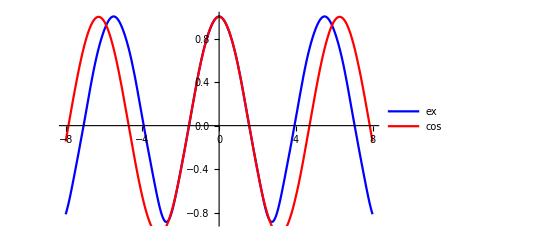

```mathematica
Show[Plot[ex,{x,-8,8},PlotStyle->Blue, PlotLegends->{"ex"}],Plot[Cos[x],{x,-8,8},PlotStyle->Red,PlotLegends->{"cos"}]]
```